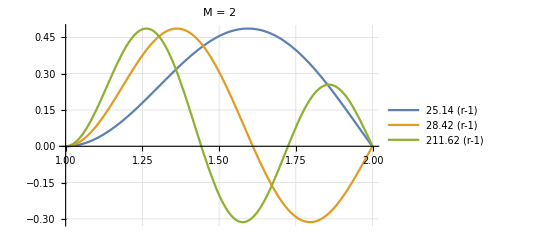

```mathematica
Plot[{BesselJ[2,5.14*(r-1)],BesselJ[2,8.42*(r-1)],BesselJ[2,11.62*(r-1)]},{r,1,2},
PlotLabel->"M = 2",
GridLines->Automatic,
PlotLegends->"Expressions",
BaseStyle->{FontSize->18},
PlotStyle->Thick]
```

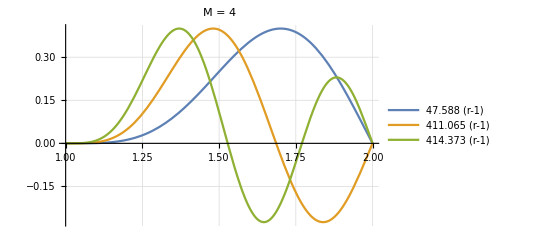

```mathematica
Plot[{BesselJ[4,7.588*(r-1)],BesselJ[4,11.065*(r-1)],BesselJ[4,14.373*(r-1)]},{r,1,2},
PlotLabel->"M = 4",
GridLines->Automatic,
PlotLegends->"Expressions",
BaseStyle->{FontSize->18},
PlotStyle->Thick]
```

```mathematica
RevolutionPlot3D[{BesselJ[2,5.14*(r-1)]*Sin[2θ]},{r,1,2},{θ,0,π/2},PlotLabel->"ϕ_(1, 1)(r,θ)"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[BesselJ[2,8.42*(r-1)]*Sin[2θ],{r,1,2},{θ,0,π/2},PlotLabel->"ϕ_(1, 2)(r,θ)"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[BesselJ[4,7.588*(r-1)]*Sin[4θ],{r,1,2},{θ,0,π/2},PlotLabel->"ϕ_(2, 1)(r,θ)"]
```

-Graphics3D-